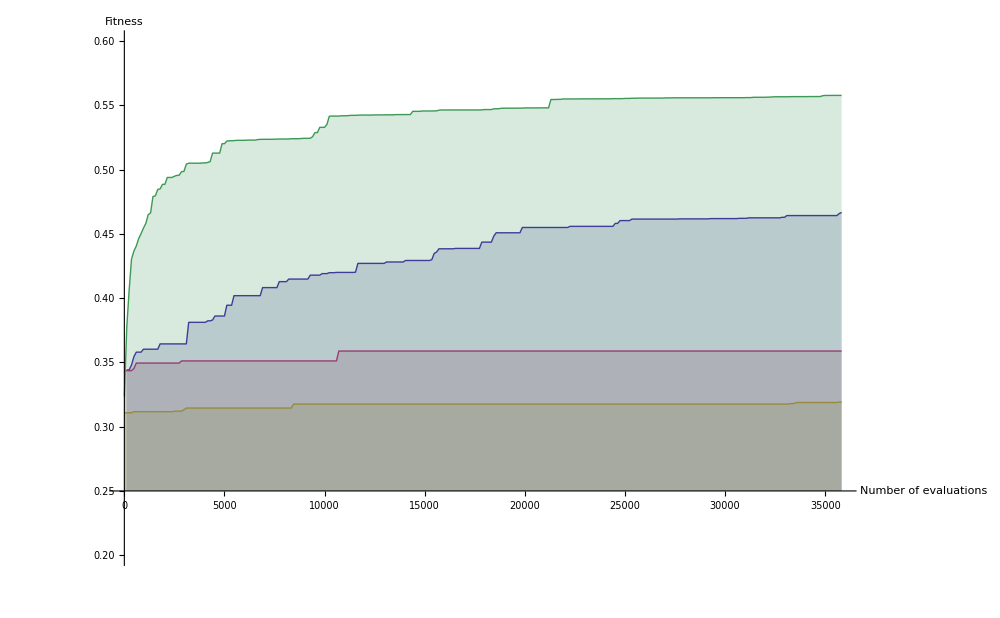

```mathematica
Needs["PlotLegends`"];

GetSeries[file_]:=Block[{line,points={},title},
title=Read[file,String];
line=Read[file,String];
While[line≠"END-SERIES",
AppendTo[points,ToExpression[RowBox[{"{",line,"}"}]]];
line=Read[file,String]
];
{title,points}
]

showplot[statsfile_]:=Block[
{file,title,dimensions,dimnames={},series={},numseries},
file = OpenRead[statsfile];
title = Read[file, String];
dimensions = Read[file, Real];
Do[AppendTo[dimnames, Read[file, String]],{dimensions}];
numseries= Read[file, Number];
Do[AppendTo[series,GetSeries[file]],{numseries}]
dimnames;
Close[file];
(*Print[series[[All,1]]]*)
If[dimensions==3,
(*Only one of these will be returned, depending on the number of dimensions*)
ListPlot3D[series[[All,2]], InterpolationOrder->3,AxesLabel -> dimnames,ColorFunction->"Rainbow",Mesh->None, PlotStyle->Thick, AxesStyle-> Thick, LabelStyle-> Large, ImageSize->1000],

ListPlot[series[[All,2]],Joined->True, InterpolationOrder->1 ,AxesLabel -> dimnames,Mesh->None,PlotRange->{.2,.6},Filling->Axis,AxesOrigin->{0,0.25} ,(*PlotLegend-> series[[All,1]],LegendPosition->{0.25,-0.45},LegendShadow->None, LegendSize-> 1,*) PlotStyle->Thick, AxesStyle-> Thick,  LabelStyle-> Large,ImageSize->1000
]]
(*,PlotLegend-> series[[All,1]] *)
]

statsfile="C:\\cygwin\\home\\deco\\trunk\\GA_TestBench\\Data Files\\Really Nice Data\\HUGE FullAverageStats(-130480562) over 1 iterations with 35820 evals 120 pop 300 gens 1 copies 6 mutations 110 crossovers 3 randoms.txt";
s2="C:\\cygwin\\home\\deco\\trunk\\GA_TestBench\\Data Files\\Really Nice Data\\MEDIUM GA_Size_Data_with_ideal_proportions_pop_goes_from_5-150_and_gen_goes_from_5-250_with_5_trials.txt";

showplot[statsfile]
showplot[s2]
```